```mathematica
BeginPackage["max"]
```

```mathematica
DataToAssociation[filename_] := 
Module[{},
data = Import[FileNameJoin[{NotebookDirectory[], filename}],"Table"];
transpose = Transpose[data];
timeData=Transpose[Rest[transpose]/. minutes_Integer:>TimeObject[{Quotient[minutes,100],Mod[minutes,100],0}]];
timeDiffTable = Table[Table[timeData[[All,j]][[i]]-timeData[[All,j]][[i-1]], {i, 2, Length[timeData]}], {j, 1, Length[Transpose[timeData]]}];
maxModeTimes = Table[Max[Commonest[timeDiffTable[[All, i]]]], {i, 1, Length[timeDiffTable[[1]]]}];
stopPairs = Table[List[First[transpose][[i-1]],First[transpose][[i]]], {i, 2, Length[maxModeTimes]+1}];
association = Association[Table[stopPairs[[i]]->maxModeTimes[[i]], {i, 1, Length[stopPairs]}]];
waiting = Association[Table[Keys[association][[i]]->
If[
(StringTake[Keys[association][[i]][[1]], -4] == "_arr" && StringTake[Keys[association][[i]][[2]], -4] == "_dep") ,
association[[Key[Keys[association][[i]]]]], Quantity[0, "Minutes"]],
{i, 1, Length[Keys[association]]}]];
travelTimeAssociation = Module[{cleaned},
cleaned = Association[];
i = 0;
While[i <Length[association],
i++;
If[waiting[[i]]==0 Quantity[, "Minutes"] && (StringTake[Keys[association][[i]][[1]], -4] == "_dep" || StringTake[Keys[association][[i]][[2]], -4] == "_arr"),
If[StringTake[Keys[association][[i]][[1]], -4] == "_dep",
AppendTo[cleaned, List[StringDrop[Keys[association][[i]][[1]], -4],Keys[association][[i]][[2]]]-> association[[Key[Keys[association][[i]]]]]],
AppendTo[cleaned, List[Keys[association][[i]][[1]],StringDrop[Keys[association][[i]][[2]], -4]]-> association[[Key[Keys[association][[i]]]]]]
],
If [waiting[[i]]==0 Quantity[, "Minutes"],
cleaned[Keys[association][[i]]] = association[[Key[Keys[association][[i]]]]],
Nothing[]],
Nothing[]];
];
cleaned
];

allStops = List[];
AppendTo[allStops, Keys[travelTimeAssociation][[1]][[1]]];
Do[AppendTo[allStops, x[[2]]],
{x, Keys[travelTimeAssociation]}
];
(*List[travelTimeAssociation, waiting, allStops]*)
travelTimeAssociation
];

SharedStops[route1_, route2_] := Intersection[Stops[route1], Stops[route2]];
```

```mathematica
x_⊕y_:=Max[x,y]
```

```mathematica
x_ ⊗y_:=x+y
```

```mathematica
mplus[x_,y_]:=MapThread[Max,{x,y}, 2]
```

```mathematica
mtimes[x_,y_]:=Inner[Plus,x,y,Max]
```

```mathematica
mpower[x_,p_]:= Module[{res},
If[p>=1,
res = x,
res = EMatrix[Length[x]]];
For[i = 2, i<=p, i++,
res = mtimes[res, x]
];
res
]
```

```mathematica
mpowerDynamic[x_, p_, kpx_] := Module[{closestBelow, pow, pows},
pows = kpx;
If[p>1,
closestBelow =Max@Select[Keys[kpx],#<=p&];
pow =pows[closestBelow];
For[i = closestBelow+1, i<=p, i++,
pow = mtimes[pow, x];
AppendTo[pows, i->pow];
];,
If[p <=0,
pow=EMatrix[Length[x]],
pow=x
];
];
List[pow, pows]
]
```

```mathematica
scalarplus[x_,y_]:=Outer[Max,{x},y]
```

```mathematica
eps=-Infinity
```

```mathematica
EpsilonMatrix[n_] := Table[Table[eps, {col, 1, n}], {row, 1, n}]
(* Returns an n x n matrix filled with Epsilon *)
```

```mathematica
EMatrix[n_]:= Table[Table[If[col == row, 0, eps], {col, 1, n}], {row, 1, n}]
(* Returns an n x n identity matrix *)
```

```mathematica
MakeNicePlaceName[rn_, s1_, s2_] :=ToString[StringJoin["p:",rn,":", s1, "+", s2]]
(* returns a formatted place name *)
```

```mathematica
MakeNiceTransitionName[rn_,q_] := ToString[StringJoin["q:",rn,":", q]]
(* returns a formatted transition name *)
```

```mathematica
MergeDirections[forward_, reverse_] := Module[{f, r, merged, nk, xS, start, end},
(* merges the forward and backward (arbitary) directions of a bus route *)
f = DataToAssociation[forward];
start = Keys[f][[1]][[1]];
r = DataToAssociation[reverse];
end = Keys[r][[1]][[1]];

Do[
nk ={StringJoin[x[[1]], If[x[[1]] ==start,"_end","_fwd"]], StringJoin[x[[2]], If[x[[2]] ==end,"_end","_fwd"]]};
f[nk] = f[x];
f[x] =.,
{x, Keys[f]}
];

Do[
nk ={StringJoin[x[[1]], If[x[[1]] ==end,"_end","_rev"]],StringJoin[x[[2]],  If[x[[2]] ==start,"_end","_rev"]]};
r[nk] = r[x];
r[x] =.,
{x, Keys[r]}
];

merged = Join[f, r];
merged
]
```

```mathematica
GetTransitionStopName[transitionString_] := StringDrop[StringSplit[transitionString, ":"][[-1]],-4];
(* returns the transition name from a "nice" formatted transition *)

GetTransitionStop[transitionString_]:=StringSplit[transitionString, ":"][[-1]];
(* returns the transition stop, including route direction from a "nice" formatted transition *)
```

```mathematica
GetTransitionRoute[transitionString_] :=StringSplit[transitionString, ":"][[2]];(* returns the transition route number from a "nice" formatted transition *)
```

```mathematica
Algorithm821[lineDataFile_, routeNumbers_]:=
(*Line data file is a list of associations, where each asscoiation corresponds to a merged version of the TT association for the forward and backward journey of a given route. So each association represents a route*)
Module[{TAPsFromRoute, Synchronization, NumberRoutes, cycleTime},
cycleTime =60 Quantity[, "Minutes"];

NumberRoutes[] := Module[{indexedAssociations},
(* returns an association with route number as key and travel time associations (route data) as values *)
indexedAssociations = Association[];
For[i=1,i<=Length[routeNumbers], i++,
indexedAssociations[routeNumbers[[i]]]= lineDataFile[[i]];
];
indexedAssociations
];

TAPsFromRoute[routeNumber_, routeAssociation_] :=Module[{startStop, endStop, cumulativeTime,nextStopCumulativeTime, modCumulative, modNextCumulative,tokens, finalHoldingTime, transitions, places, arcs},
(* returns the transitions, arcs, and place of an individual route *)
transitions = List[];
places = Association[];
arcs = List[];
startStop = Keys[routeAssociation][[1]][[1]];
endStop = Keys[routeAssociation][[-1]][[1]];
AppendTo[transitions,MakeNiceTransitionName[routeNumber, startStop]];
cumulativeTime = 0 Quantity[, "Minutes"];
Do[
AppendTo[transitions,MakeNiceTransitionName[routeNumber, pair[[2]]]];
nextStopCumulativeTime =cumulativeTime + routeAssociation[[Key[pair]]];
modCumulative = Mod[cumulativeTime, cycleTime];
modNextCumulative = Mod[nextStopCumulativeTime, cycleTime];
tokens = Ceiling[(routeAssociation[[Key[pair]]] + modCumulative - modNextCumulative)/cycleTime];
AppendTo[places,  MakeNicePlaceName[routeNumber, pair[[1]],pair[[2]]]->List[routeAssociation[[Key[pair]]], tokens]];
cumulativeTime = nextStopCumulativeTime;
AppendTo[arcs, MakeNiceTransitionName[routeNumber, pair[[1]]]->Keys[places][[-1]]];
AppendTo[arcs, Keys[places][[-1]]->MakeNiceTransitionName[routeNumber, pair[[2]]]];
,
{pair, Keys[routeAssociation][[1;;-2]]}
];
finalHoldingTime =routeAssociation[[Key[List[endStop, StringReplace[startStop, {"fwd"->"rev"}]]]]];
nextStopCumulativeTime =cumulativeTime + finalHoldingTime;
modCumulative = Mod[cumulativeTime, cycleTime];
modNextCumulative = Mod[nextStopCumulativeTime, cycleTime];
tokens = Ceiling[(finalHoldingTime + modCumulative - modNextCumulative)/cycleTime];
AppendTo[places, MakeNicePlaceName[routeNumber,endStop, startStop]->List[finalHoldingTime, tokens] ]; (*make sure this is indeed the last one*)
AppendTo[arcs, MakeNiceTransitionName[routeNumber, endStop]->MakeNicePlaceName[routeNumber, endStop, startStop]];
AppendTo[arcs, MakeNicePlaceName[routeNumber, endStop, startStop]->MakeNiceTransitionName[routeNumber, startStop]];
List[transitions, arcs, places]
];

Synchronization[routePlaces_] := Module[{arcs, places, indexedRoutes},
(* returns the arcs and places between routes with shared stops *)
indexedRoutes = NumberRoutes[];
arcs=List[];
places=Association[];
Do[
Do[
Do[
Do[
If[assoc1 != assoc2,
If[StringDrop[key1[[2]],-4]==StringDrop[key2[[2]],-4],
(* add arc from previous stop on origin line to new place *)
(* add arc from new place to shared stop on the other line *)
placeWeWant = MakeNicePlaceName[assoc2, key2[[1]], key2[[2]] ];
AppendTo[places, MakeNicePlaceName[StringJoin[assoc2, "->", assoc1], key2[[1]], key1[[2]]]->routePlaces[[placeWeWant]]];
AppendTo[arcs, MakeNiceTransitionName[assoc2,key2[[1]]]->Keys[places][[-1]]];
AppendTo[arcs, Keys[places][[-1]]->MakeNiceTransitionName[assoc1, key1[[2]]]];,
Nothing[]
];
Nothing[]
];,
{key2,Keys[indexedRoutes[[Key[assoc2]]]]}
],
{key1,Keys[indexedRoutes[[Key[assoc1]]]]}
],
{assoc2,Keys[indexedRoutes]}
],
{assoc1,Keys[indexedRoutes]}
];
List[arcs, places]
];

transitions = List[];
places = Association[];
arcs = List[];

(* find transitions, arcs, and places for all routes *);
For[i=1, i<=Length[lineDataFile], i++,
temps= TAPsFromRoute[routeNumbers[[i]], lineDataFile[[i]]];
transitions = Join[transitions, temps[[1]]];
arcs = Join[arcs, temps[[2]]];
places = Join[places, temps[[3]]];
];

(* find arcs and places between routes *);
sync = Synchronization[places];
arcs = Join[arcs, sync[[1]]];
places = Join[places, sync[[2]]];

List[transitions, arcs, places]
]
```

```mathematica
MatrixFromPetriNet[transitions_, arcs_, places_] := Module[{AMatrices, GetPlaceBetween, A0Star, MatrixABlocks, ATwiddle},
(*reccurence relation*)
GetPlaceBetween[t1_, t2_] :=Module[{p},
If[
GetTransitionRoute[t1]==GetTransitionRoute[t2],

p =MakeNicePlaceName[GetTransitionRoute[t1], GetTransitionStop[t1], GetTransitionStop[t2]],

p = MakeNicePlaceName[StringJoin[GetTransitionRoute[t1], "->", GetTransitionRoute[t2]], GetTransitionStop[t1], GetTransitionStop[t2]]
];
p
];

AMatrices[]:=Module[{maxTokens, p, row, matrix, matrices},
maxTokens = 0;
Do[
If[x[[2]]>maxTokens,
maxTokens=x[[2]],
Nothing[]
],
{x, places}];

matrices = List[];

For[m=0, m<=maxTokens, m++, 
matrix = List[];
Do[
row =List[];
Do[
p =GetPlaceBetween[j,i];
If[MemberQ[Keys[places], p],
p = places[[p]];
If[p[[2]]==m,
AppendTo[row, (p[[1]]/Quantity[, "Minutes"])],
AppendTo[row, eps ]
],
AppendTo[row, eps ];
];,
{j, transitions}];
AppendTo[matrix, row];
,
{i, transitions}];
AppendTo[matrices, matrix];
];
matrices
];

A0Star[A0_] :=Module[{R, knownPowers,powerAndKnown, mp},
R =EMatrix[Length[A0]];
knownPowers=Association[1->A0];
For[l=1, l<=Length[transitions], l=l+1,
powerAndKnown= mpowerDynamic[A0, l, knownPowers];
mp = powerAndKnown[[1]];
knownPowers =powerAndKnown[[2]];
Print[Keys[knownPowers]];
R=mplus[R,mp];
];
R
];

MatrixABlocks[ AMatrixList_, A0S_] :=Module[{s, blocks, a},
blocks = List[];
Do[
a= mtimes[A0S, A];
AppendTo[blocks,a],
{A, Drop[AMatrixList, 1]}
];
blocks
];

ATwiddle[blocks_]:=Module[{atwid, flatBlocks, row, rows, blockLen},
If[Length[blocks]==1,
atwid = blocks[[1]],
blockLen = Length[blocks[[1]]];
flatBlocks = ArrayFlatten[{blocks}];
rows=flatBlocks;
For [i=1, i<=Length[blocks]-1,i++,
row =Table[EpsilonMatrix[blockLen], Length[blocks]];
row =ReplacePart[row, i->EMatrix[blockLen]];
rows =Join[rows, ArrayFlatten[{row}], 1];
];
atwid =rows;
];
atwid
];

Comp[]:=Module[{matrixList, A0S, matrixABlocks, matrix},
matrixList = AMatrices[];
A0S = A0Star[matrixList[[1]]];
matrixABlocks = MatrixABlocks[matrixList, A0S];
matrix = ATwiddle[matrixABlocks];

matrix
];
Comp[]
]
```

```mathematica
EndPackage[]
```

```mathematica
b1 = MergeDirections["1_Danestone_RGU.txt", "1_RGU_Danestone.txt"];
b2 = MergeDirections["2_Ashwood_RGU.txt", "2_RGU_Ashwood.txt"];
b3 = MergeDirections["3_Cove_Mastrick.txt", "3_Mastrick_Cove.txt"];
b11 = MergeDirections["11_Northfield_Woodend.txt", "11_Woodend_Northfield.txt"];
b12 = MergeDirections["12_Heathryfold_Torry.txt", "12_Torry_Heathryfold.txt"];
b13 = MergeDirections["13_Golf_Links_Scatterburn.txt", "13_Scatterburn _Golf_Links.txt"];
b15 = MergeDirections["15_Balnagask_Circle_Countesswells.txt", "15_Countesswells_Balnagask_Circle.txt"];
b17 = MergeDirections["17_Dyce_Faulds_Gate.txt", "17_Faulds_Gate_Dyce.txt"];
b18 = MergeDirections["18_Dyce_Redmoss.txt", "18_Redmoss_Dyce.txt"];
b19 = MergeDirections["19_Culter_Tillydrone.txt", "19_Tillydrone_Culter.txt"];
b20 = MergeDirections["20_Guild_str_Hillhead.txt", "20_Hillhead_Guild_str.txt"];
b23 = MergeDirections["23_Raasay_Gardens_Heathryfold.txt",  "23_Heathryfold_Raasay_Gardens.txt"];
```

```mathematica
TAPs=Algorithm821[{b11, b19}, {"11", "19"}];
```

```mathematica
mtx =MatrixFromPetriNet[TAPs[[1]], TAPs[[2]], TAPs[[3]]];
```

{1}

{1,2}

{1,2,3}

{1,2,3,4}

{1,2,3,4,5}

{1,2,3,4,5,6}

{1,2,3,4,5,6,7}

{1,2,3,4,5,6,7,8}

{1,2,3,4,5,6,7,8,9}

{1,2,3,4,5,6,7,8,9,10}

{1,2,3,4,5,6,7,8,9,10,11}

{1,2,3,4,5,6,7,8,9,10,11,12}

{1,2,3,4,5,6,7,8,9,10,11,12,13}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}

```mathematica
Export[FileNameJoin[{NotebookDirectory[], "matrix11-19.txt"}], mtx]
```

E:\Dokumentumok\Uni\2023-II\MX4553\Project\maxplusbus\matrix11-19.txt

```mathematica
Dimensions[mtx]
```

{22,22}

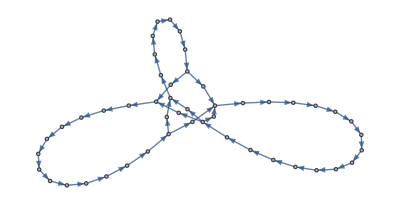

```mathematica
Graph[TAPs[[2]]]
```

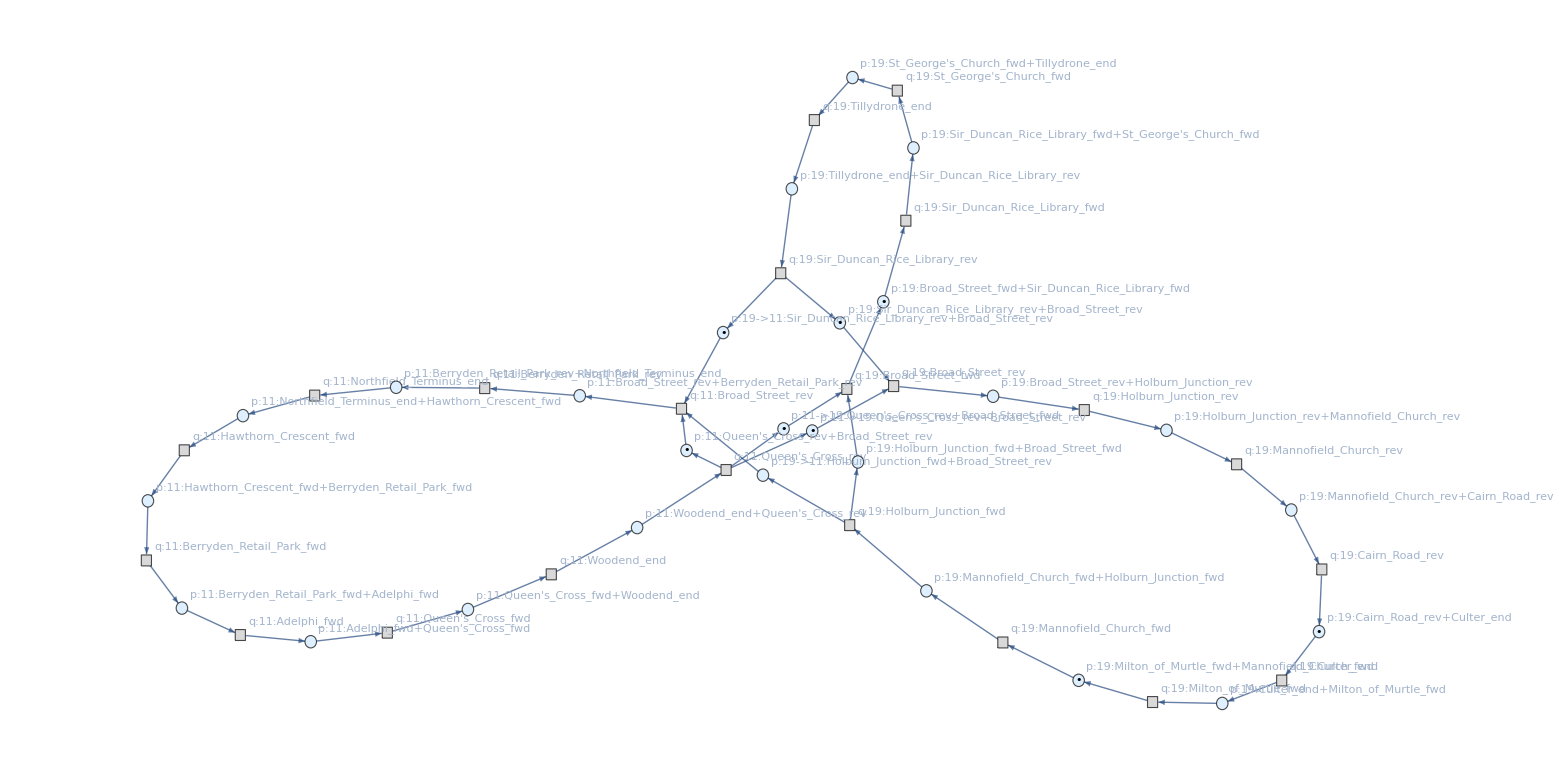

```mathematica
placesList=Keys[TAPs[[3]]];
transitionsList=TAPs[[1]];
arcsList=TAPs[[2]];
initialMarkings=#[[2]]&/@Values[TAPs[[3]]];
petriNet=ResourceFunction["MakePetriNet"][placesList,transitionsList,arcsList, initialMarkings];
petriNet["LabeledGraph"]
```

```mathematica
TAPs[[1]]
```

{q:11:Northfield_Terminus_end,q:11:Hawthorn_Crescent_fwd,q:11:Berryden_Retail_Park_fwd,q:11:Adelphi_fwd,q:11:Queen's_Cross_fwd,q:11:Woodend_end,q:11:Queen's_Cross_rev,q:11:Broad_Street_rev,q:11:Berryden_Retail_Park_rev,q:19:Culter_end,q:19:Milton_of_Murtle_fwd,q:19:Mannofield_Church_fwd,q:19:Holburn_Junction_fwd,q:19:Broad_Street_fwd,q:19:Sir_Duncan_Rice_Library_fwd,q:19:St_George's_Church_fwd,q:19:Tillydrone_end,q:19:Sir_Duncan_Rice_Library_rev,q:19:Broad_Street_rev,q:19:Holburn_Junction_rev,q:19:Mannofield_Church_rev,q:19:Cairn_Road_rev}

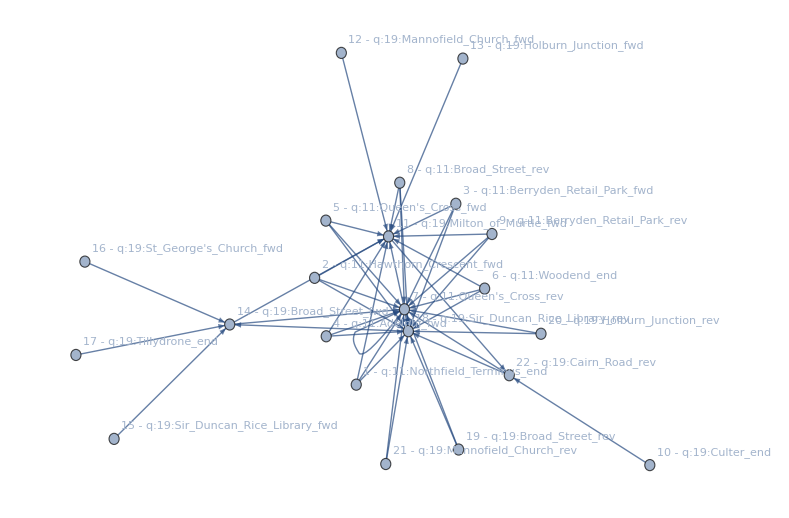

```mathematica
ReplaceInRows[matrix_,oldValue_,newValue_]:=Replace[matrix,oldValue->newValue,{2}]
ChangeNonZeroValues[matrix_,newValue_]:=matrix/. x_/;x!=eps:>newValue
noZeros = ChangeNonZeroValues[mtx, 1];
noInfi = ReplaceInRows[noZeros, -eps, 0] ;
AdjacencyGraph[noInfi, {VertexLabels->Table[i->StringJoin[ToString[i], " - ",TAPs[[1]][[i]]],{i,1,Length[TAPs[[1]]]}]}]
```

```mathematica
mtx // MatrixForm
```

(-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 33. | -∞ | -∞ | -∞ | 56. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 38. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 41. | -∞ | -∞ | -∞ | 64. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 46. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 50. | -∞ | -∞ | -∞ | 73. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 55. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 61. | -∞ | -∞ | -∞ | 84. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 66. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 73. | -∞ | -∞ | -∞ | 96. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 78. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 81. | -∞ | -∞ | -∞ | 104. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 86. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 89. | -∞ | -∞ | -∞ | 112. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 94. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | 33. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 21. | -∞ | -∞ | -∞ | 44. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 26. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 13.
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 27.
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 24. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | 33. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 14. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 17. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 20. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 28. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 10. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 15. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 17. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 22. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 28. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 33. | -∞ | -∞ | -∞ | -∞
-∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 39. | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | -∞ | 44. | -∞ | -∞ | -∞ | -∞)

```mathematica
xnext = mtimes[mpower[mtx, 1], {eps, eps, eps, eps, eps, eps, 0, eps, eps, eps, 1, eps, eps, eps, 2, eps, eps, 0, eps, eps, eps, eps}]
```

{57.,65.,74.,85.,97.,105.,113.,34.,45.,-∞,-∞,16.,25.,34.,-∞,-∞,-∞,-∞,15.,22.,33.,44.}

```mathematica
Prepend[List[xnext], TAPs[[1]]] // Transpose // MatrixForm
```

(q:11:Northfield_Terminus_end | 57.
q:11:Hawthorn_Crescent_fwd | 65.
q:11:Berryden_Retail_Park_fwd | 74.
q:11:Adelphi_fwd | 85.
q:11:Queen's_Cross_fwd | 97.
q:11:Woodend_end | 105.
q:11:Queen's_Cross_rev | 113.
q:11:Broad_Street_rev | 34.
q:11:Berryden_Retail_Park_rev | 45.
q:19:Culter_end | -∞
q:19:Milton_of_Murtle_fwd | -∞
q:19:Mannofield_Church_fwd | 16.
q:19:Holburn_Junction_fwd | 25.
q:19:Broad_Street_fwd | 34.
q:19:Sir_Duncan_Rice_Library_fwd | -∞
q:19:St_George's_Church_fwd | -∞
q:19:Tillydrone_end | -∞
q:19:Sir_Duncan_Rice_Library_rev | -∞
q:19:Broad_Street_rev | 15.
q:19:Holburn_Junction_rev | 22.
q:19:Mannofield_Church_rev | 33.
q:19:Cairn_Road_rev | 44.)

```mathematica
Length[xnext]
Length[TAPs[[1]]]
```

22

22

```mathematica
mtimes[mpower[mtx, 2], {eps, eps, eps, eps, eps, eps, 0, eps, eps, eps, eps, eps, eps, eps, eps, eps, eps, eps, eps, eps, eps, eps}]
```

{122.,130.,139.,150.,162.,170.,178.,99.,110.,52.,66.,-∞,-∞,99.,24.,27.,30.,38.,99.,106.,117.,128.}

```mathematica
TAPs[[1]][[-5]]
```

q:19:Sir_Duncan_Rice_Library_rev

```mathematica
TimeObject[{0,#,0}] &/@ xnext
```

{00:33:00TimeObject[{0,33,0.},Instant],00:41:00TimeObject[{0,41,0.},Instant],00:50:00TimeObject[{0,50,0.},Instant],01:01:00TimeObject[{1,1,0.},Instant],01:13:00TimeObject[{1,13,0.},Instant],01:21:00TimeObject[{1,21,0.},Instant],01:29:00TimeObject[{1,29,0.},Instant],00:10:00TimeObject[{0,10,0.},Instant],00:21:00TimeObject[{0,21,0.},Instant]}

```mathematica
{Quotient[minutes,100],Mod[minutes,100],0}
```

```mathematica
Length[TAPs[[1]]]
```

138

```mathematica
Max[initialMarkings]
```

1